## Read Me

This code is an example of how to implement the amoeba projection for any toric polygon. Let (x, y) be the C^* coordinates used for expressing the Newton polygon of the toric diagram. The amoeba projection is obtained as:

			 (x, y) -> (r_x,r_y) = (log|x|, log |y|),

where (r_x,r_y) are now real variables.
 The algorithms are based on [1, 2]. There are two functions defined in this notebok:

- AmoebaData[f[x,y], Ntheta ,NR, xVals]
- AmoebaContourData[f[x,y], Ntheta, NR, xVals]

Here:
- f[x, y] is a toric polygon expressed in terms of variables x and y
- xVals = {{r_x_min, r_x_max}, {r_y_min, r_y_max}} is the rectangular domain of r_x and r_y used in the projection
- NR and Ntheta correspond to the number of data points for the absolute value (R) and the angle (theta) of the complex variable in the amoeba plane -- i.e. the more points, the denser the projection.

For more details on the implementation, we refer to [1].

References:
[1] D. Bogdanov, A. A. Kytmanov and T. M. Sadykov, Algorithmic computation of polynomial amoebas, in International Workshop on Computer Algebra in Scientific Computing, pp. 87-100, Springer, 2016.
[2] D. Bogdanov, Online Amoeba Tool, http://dvbogdanov.ru/amoeba

## Definitions

### Amoeba projection

```mathematica
SetAttributes[{AmoebaData},HoldAll];
AmoebaData[f_[x_,y_],N1_ ,N2_,Vals_]:=Module[{Ntheta=N1,NR=N2,xVals=Vals},
degree = {Exponent[f[x,y],x], Exponent[f[x,y],y]};
Theta=Array[#&,Ntheta ,{0,2Pi}]//N;
plots=ConstantArray[1,{2,NR}];
For[type=1,type≤2,type++,
LogR=Array[#&,NR,xVals[[type]]]//N; 
Ones=ConstantArray[1,Ntheta*degree[[type]]];
Rho={};
For[j=1,j≤NR,j++,
	For[i=1,i≤Ntheta,i++,
	If[type==1, 
	roots=y/.{ToRules[Roots[f[Exp[LogR[[j]]] E^(I Theta[[i]]),y]==0,y]]}//N,
	roots=x/.{ToRules[Roots[f[x,Exp[LogR[[j]]] E^(I Theta[[i]])]==0,x]]}]//N;
	AppendTo[Rho,Log[Abs[roots]]]//Flatten
	];
	If[type==1,plots[[1,j]]=Transpose@{LogR[[j]]*Ones,Rho//Flatten},
plots[[2,j]]=Transpose@{Rho//Flatten,LogR[[j]]*Ones}];
	Rho={};
	]
];
plots
];
```

### Amoeba contour

```mathematica
SetAttributes[{AmoebaContourData},HoldAll];
AmoebaContourData[f_[x_,y_],N2_,Vals_]:=Module[{NR=N2,xVals=Vals},
degree = {Exponent[f[x,y],x], Exponent[f[x,y],y]};
plots=ConstantArray[1,{2,NR}];
For[type=1,type≤2,type++,
LogR=Array[#&,NR,xVals[[type]]]//N; 
Ones=ConstantArray[1,degree[[type]]];
Rho={};
For[j=1,j≤NR,j++,
	If[type==1, 
	roots=y/.{ToRules[Roots[f[Exp[LogR[[j]]],y]==0,y]]}//N,
	roots=x/.{ToRules[Roots[f[x,Exp[LogR[[j]]]]==0,x]]}]//N;
	AppendTo[Rho,Log[Abs[roots]]]//Flatten;
	If[type==1,plots[[1,j]]=Transpose@{LogR[[j]]*Ones,Rho//Flatten},
plots[[2,j]]=Transpose@{Rho//Flatten,LogR[[j]]*Ones}];
	Rho={};
	]
];
plots
];
```

## Projections

### P^2 (SW curve of E_0 SCFT)

```mathematica
ClearAll; Clear[g2,g3,U,Δ,J,L];
 g2[U_]:=-3/4 U(8-9 U^3)//Simplify;
g3[U_]:=1/8(-27 U^6+36 U^3-8)//Simplify;
Δ[U_]:=g2[U]^3-27 g3[U]^2//Simplify
J[U_]:=g2[U]^3/(g2[U]^3-27 g3[U]^2)//Simplify
Solve[Δ[U]==0,U]
```

{{U→1},{U→-(-1)^(1/3)},{U→(-1)^(2/3)}}

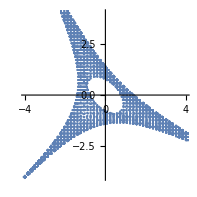

```mathematica
Clear[Ntheta ,NR,xVals,f,x,y,u];
Ntheta = 40;NR=50;xVals={ {-4,4},{-4,4}};
u=E^(I Pi/6);
f[x_,y_]:=x+y-3u x y+x^2 y^2;
plots=AmoebaData[f[x,y],Ntheta ,NR,xVals];

Clear[j];
PLT1[j_]:=ListPlot[plots[[1,j]],PlotMarkers->{Automatic,2},AspectRatio->1];
PLT2[j_]:=ListPlot[plots[[2,j]],PlotMarkers->{Automatic,2},AspectRatio->1];
Show[Table[{PLT1[j],PLT2[j]},{j,1,NR}]//Flatten,PlotRange->xVals]
```

### P^1 x P^1 (SW curve of E_1 SCFT)

```mathematica
ClearAll; Clear[g2,g3,U,λ,Δ,J,L];
g2[U_]:=1/12 (16+U^4+16 (-1+λ) λ-8 U^2 (1+λ));
g3[U_]:=-4/27 (-2+U^6/32+3 λ+3 λ^2-2 λ^3-3/8 U^4 (1+λ)+3/4 U^2 (2+λ+2 λ^2));
Δ[U_]:=g2[U]^3-27 g3[U]^2//Simplify
J[U_]:=g2[U]^3/(g2[U]^3-27 g3[U]^2)//Simplify
Sols=Solve[Δ[U]==0,U]
```

{{U→-2 (-1+√λ)},{U→2 (-1+√λ)},{U→-2 (1+√λ)},{U→2 (1+√λ)}}

```mathematica
Clear[λ]; λ=-1;
Sols//N

(* toric curve: *)
((λ^(1/2)(1/t+t)+1/w+w-U)*t*w//Expand)/.{t-> x, w-> y}
```

{{U→2.-2. ⅈ},{U→-2.+2. ⅈ},{U→-2.-2. ⅈ},{U→2.+2. ⅈ}}

x+ⅈ y-U x y+ⅈ x^2 y+x y^2

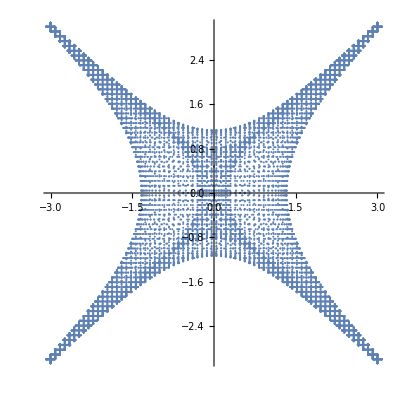

```mathematica
Clear[Ntheta ,NR,xVals,f,x,y,u];
Ntheta = 50;NR=70;xVals={ {-3,3},{-3,3}};
u=-1.5-0.5I;
f[x_,y_]:=x+ⅈ y-u x y+ⅈ x^2 y+x y^2;
plots=AmoebaData[f[x,y],Ntheta ,NR,xVals];

Clear[j];
PLT1[j_]:=ListPlot[plots[[1,j]],PlotMarkers->{Automatic,2},AspectRatio->1];
PLT2[j_]:=ListPlot[plots[[2,j]],PlotMarkers->{Automatic,2},AspectRatio->1];
Show[Table[{PLT1[j],PLT2[j]},{j,1,NR}]//Flatten,PlotRange->xVals,AspectRatio->1]
```

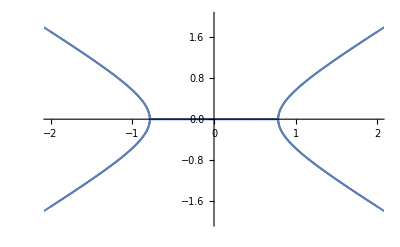

```mathematica
Clear[Ntheta ,NR,xVals,f,x,y];
NR=500;xVals={ {-2,2},{-2,2}};

f[x_,y_]:=x+0.7549834435270749 y+0.7549834435270749 x^2 y+x y^2;
plots=AmoebaContourData[f[x,y],NR,xVals];

Clear[j];
PLT1[j_]:=ListPlot[plots[[1,j]],PlotMarkers->{Automatic,2}];
PLT2[j_]:=ListPlot[plots[[2,j]],PlotMarkers->{Automatic,2}];
Show[Table[{PLT1[j],PLT2[j]},{j,1,NR}]//Flatten,PlotRange->xVals]
```